```mathematica
ClearAll["Global`*"]; 
kMax = 5; 
kiMax = IntegerPart[kMax] + 1; 
base = {{-1, 1, 1}, {1, -1, 1}, {1, 1, -1}}; 
rcpltc = {}; 
For[i = -2*kiMax, i < 2*kiMax, For[j = -2*kiMax, j < 2*kiMax, 
     For[k = -2*kiMax, k < 2*kiMax, If[Norm[{i, j, k} . base] < kMax, rcpltc = Join[rcpltc, {{i, j, k} . base}]]; k++]; j++]; i++]; 
rcpltc = SortBy[rcpltc, Norm]; 
n = Length[rcpltc]
Norm[rcpltc[[n]]]^2
```

137

19

```mathematica
NormSqr[x_]:=x⟦1⟧^2+x⟦2⟧^2+x⟦3⟧^2;
V1[q_]:=If[q==3,-.23,If[q==8,.01,If[q==11,.06,0.]]];
V2[q_]:=If[q==3,.07,If[q==4,.05,If[q==11,.01,0.]]];
```

```mathematica
bohradiuspm = 52.917721067; 
lc = 564.35/bohradiuspm
sce = (2*(Pi/lc))^2; 
tau = (Pi/4)*{1, 1, 1}; 
H = Table[If[i < j, V1[NormSqr[rcpltc[[i]] - rcpltc[[j]]]]*Cos[(rcpltc[[i]] - rcpltc[[j]]) . tau] + V2[NormSqr[rcpltc[[i]] - rcpltc[[j]]]]*I*
       Sin[(rcpltc[[i]] - rcpltc[[j]]) . tau], 0], {i, n}, {j, n}]; 
H = H + ConjugateTranspose[H]; 
Ek[kk_] := Module[{HH}, HH = H + DiagonalMatrix[sce*Array[NormSqr[rcpltc[[#1]] + kk] & , n]]; Sort[Eigenvalues[HH]]];
```

10.6647

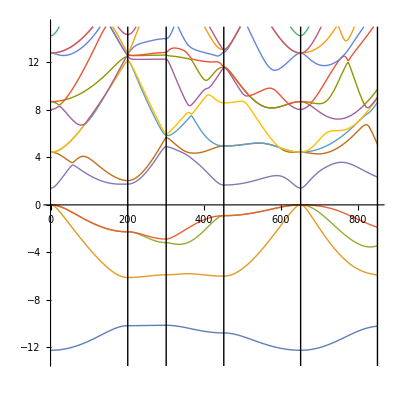

```mathematica
bas = Ek[{0, 0, 0}]; 
bass = bas[[4]]; 
bas = 13.605693009*(bas - bas[[4]]); 
k = {{0, 0, 0}, {1, 0, 0}, {1, 0, 0.5}, {0.5, 0.5, 0.5}, {0, 0, 0}, {0.75, 0.75, 0}}; 
np = {20, 10, 15, 20, 20}*10; 
sl = Array[Sum[np[[it]], {it, 1, #1}] & , Length[np]]; 
erk = ParallelTable[Table[13.605693009*(Ek[k[[jj]] + ii*((k[[jj + 1]] - k[[jj]])/np[[jj]])] - bass), {ii, 1, np[[jj]], 1}], {jj, 1, Length[np]}]; 
erk = Flatten[erk, 1]; 
erk = Join[{bas}, erk]; 
lines = {Array[Line[{{sl[[#1]] + 1, -15}, {sl[[#1]] + 1, 15}}] & , Length[np]]}; 
ListLinePlot[Take[Transpose[erk], {1, 18}], PlotRange -> {-13, 15}, AspectRatio -> 1, PlotStyle -> Thin, Epilog -> lines]
```

```mathematica
SetDirectory[NotebookDirectory[]]; 
nn = 17; 
p = Take[Transpose[erk], {1, nn}]; 
cmd = ""; 
For[i = 1, i < nn, S = "\\draw[OliveGreen] "; For[j = 1, j <= Length[p[[i]]], 
     S = StringJoin[S, "(", ToString[j - 1], ",", ToString[p[[i,j]], InputForm], ") -- "]; j++]; S = StringDrop[S, -4]; S = StringJoin[S, ";\n"]; 
    cmd = StringJoin[cmd, S]; i++]; 
For[i = 1, i < Length[np], S = "\\draw "; S = StringJoin[S, "(", ToString[sl[[i]]], ",", ToString[-13], ") -- ", "(", ToString[sl[[i]]], ",", ToString[15], 
      ")"]; S = StringJoin[S, ";\n"]; cmd = StringJoin[cmd, S]; i++]; 
cmd = StringReplace[cmd, "*^" -> "E"]; 
cmd = StringJoin["\\begin{axis}[xmin=0,xmax=", ToString[Length[erk] - 1], ",ymin=-13,ymax=15,xtick=", ToString[Join[{0}, sl]], 
    ",xticklabels={$\\Gamma$,X,W,L,$\\Gamma$,K,X},ylabel={$E$ ($e$V)}]\n", cmd, "\\end{axis}"]; 
Export["GaAsEmpr.txt", cmd]
```

GaAsEmpr.txt